```mathematica
(*  Read the file as pairs of values (x,y) *)
(*  One day I will figure out how to say HERE *)
```

```mathematica
xy = ReadList [ "/Users/jburkardt/public_html/math_src/graphics_examples/lynx.txt", {Number,Number} ]
```

{{1821,269},{1822,321},{1823,585},{1824,871},{1825,1475},{1826,2821},{1827,3928},{1828,5943},{1829,4950},{1830,2577},{1831,523},{1832,98},{1833,184},{1834,279},{1835,409},{1836,2285},{1837,2685},{1838,3409},{1839,1824},{1840,409},{1841,151},{1842,45},{1843,68},{1844,213},{1845,546},{1846,1033},{1847,2129},{1848,2536},{1849,957},{1850,361},{1851,377},{1852,225},{1853,360},{1854,731},{1855,1638},{1856,2725},{1857,2871},{1858,2119},{1859,684},{1860,299},{1861,236},{1862,245},{1863,552},{1864,1623},{1865,3311},{1866,6721},{1867,4254},{1868,687},{1869,255},{1870,473},{1871,358},{1872,784},{1873,1594},{1874,1676},{1875,2251},{1876,1426},{1877,756},{1878,299},{1879,201},{1880,229},{1881,469},{1882,736},{1883,2042},{1884,2811},{1885,4431},{1886,2511},{1887,389},{1888,73},{1889,39},{1890,49},{1891,59},{1892,188},{1893,377},{1894,1292},{1895,4031},{1896,3495},{1897,587},{1898,105},{1899,153},{1900,387},{1901,758},{1902,1307},{1903,3465},{1904,6991},{1905,6313},{1906,3794},{1907,1836},{1908,345},{1909,382},{1910,808},{1911,1388},{1912,2713},{1913,3800},{1914,3091},{1915,2985},{1916,3790},{1917,674},{1918,81},{1919,80},{1920,108},{1921,229},{1922,399},{1923,1132},{1924,2432},{1925,3574},{1926,2935},{1927,1537},{1928,529},{1929,485},{1930,662},{1931,1000},{1932,1590},{1933,2657},{1934,3396}}

```mathematica
(*  Create the image *)
```

```mathematica
g1 = ListPlot [ xy, PlotJoined->True, Epilog->{PlotStyle->PointSize[0.02], Map[Point,xy]}, DisplayFunction->Identity, PlotLabel->"Lynx Population Records",
FrameLabel->{"<--- Year --->","<--- Lynx Harvest --->"},Frame->{True,True,True,True},GridLines->{Automatic,Automatic},PlotRange->{{1820.0,1940.0},{0.0,7000.0}}];
```

```mathematica
(* Display the image *)
```

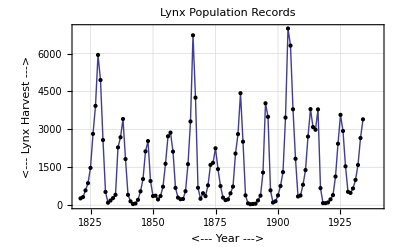

```mathematica
Show [ g1 ]
```

```mathematica
(* Export the image. *)
(* I have to say HERE using a huge string *)
```

```mathematica
Export["/Users/jburkardt/public_html/math_src/graphics_examples/lynx.png", g1, "PNG" ]
```

/Users/jburkardt/public_html/math_src/graphics_examples/lynx.png